```mathematica
SEMINARSKA NALOGA
```

```mathematica
FactorInteger[45]
FactorInteger[48]
FactorInteger[60]
```

{{3,2},{5,1}}

{{2,4},{3,1}}

{{2,2},{3,1},{5,1}}

```mathematica
Rešitev naloge 1.1
Razcep števila 45 je 3 3 5.
Razcep števila 48 je 2 2 2 2 3 3 3.
Razcep števila 60 je 2 2 3 5.
```

```mathematica
(GCD[45,48]/GCD[48,60] - GCD[11,23]/LCM[4,10])*LCM[5,20]
```

4

```mathematica
Rešitev naloge 1.2
Rešitev izraza je 4.
```

```mathematica
Daljica[A_, B_];
Dolzina[Daljica[A_, B_]] := Norm[B - A]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
d = Daljica[{-1, -2}, {5, 3}];
EnacbaNosilke[d]
```

y==-7/6+(5 x)/6

```mathematica
Sedaj smo izračunali premico, sedaj pa bomo koeficient premice vstavili v enačbo za tangens kota med dvema premicama, kjer bo druga premica kar abscisna os y = 0.
```

```mathematica
tan = Abs[(5/6-0)/1+0*5/6];
φ = N[ArcTan[tan]/Degree];
Round[φ,0.01]
```

39.81

```mathematica
Rešitev naloge 2
Enačba premice je y = 5/6*x-7/6.
Ostri kot, ki ga premica določa z absciso pa meri 39,81 °.
```

```mathematica
ClearAll[a, b];
Simplify[(a*b^2)^2]
Expand[(a+b^2)^2]
Simplify[((a^1b^2)/((a^1b^1)^3))]
Simplify[Sqrt[a^1]*CubeRoot[a^1b^1]]
TraditionalForm[√a(ab)^(1/3)]
Simplify[Sqrt[b^2],Element[b,Reals]]
```

a^2 b^4

a^2+2 a b^2+b^4

1/(a^2 b)

√a (a b)^(1/3)

√a ab^(1/3)

Abs[b]

```mathematica
Rešitev naloge 3
Ob poenostavitvi izrazov pogledamo možnosti, ki so nam ponujene, pri čemer upoštevamo različne ampak ekvivalentne zapise, npr 1/(a^2 b) = a^-2 b^-1.
Pravilno izpolnjena tabela izgleda takole.
```

```mathematica
a1 =7;
a7 = 448;
d = (a7-a1)/6
q = (a7/a1)^(1/6)
```

147/2

2

```mathematica
ClearAll[n, f]
f[x_] := 7 + x*d
Map[f, {0,1,2,3,4,5,6}]
```

{7,9,11,13,15,17,19}

```mathematica
Rešitev naloge 4.a)
To je prvih 7 členov aritmetičnega zaporedja.
```

```mathematica
ClearAll[n, g]
g[x_] := 7 *q^(x-1)
Map[g, {1,2,3,4,5,6,7}]
```

{7,14,28,56,112,224,448}

```mathematica
Rešitev naloge 4.b)
To je prvih 7 členov geometrijskega zaporedja.
```

```mathematica
Manipulate[Plot[b*(x-π/4)^2,{x,-10,10}],{b,-2,5}]
```

```mathematica
Preden se lotimo naloge si poglejmo tale manipulativni graf, ki nam omogoča opazovati spreminjanje grafa funkcije g glede na izbrani parameter b. V kodi sem omejila b med števili -2 in 5. Vidimo, da če je b = -2, je graf obrnjen navzdol. Ko je b pozitiven, je graf obrnjen navzgor in ko se b veča, graf hitreje narašča. Sedaj se pa vrnimo k nalogi.
```

```mathematica
Rešitev naloge 1.1
Definicijski območji za obe funkciji sta enaki in sicer so to kar vsa realna števila.
Zaloga vrednosti za funkcijo cos je [-1, 1], ker pa je v funkciji f cosinus premaknjen za a, je končna rešitev [a - 1, a + 1].
Zaloga vrednosti funkcije g je pa interval od 0 do neskončno, kot vemo iz znanja o kvadratni funkciji.
Pravilno izpolnjena tabela torej izgleda takole:
```

```mathematica
ClearAll[a, b, f, g]
f[x_]:= Cos[2*x] +a;
g[x_] := b*(x-π/4)^2;
Solve[{f[0]==g[0],f[π/4] == g[π/4]},{a,b}]
```

{{a→0,b→16/π^2}}

```mathematica
Rešitev naloge 1.2
Rešili smo sistem 2 enačb z dvema neznankama in dobili rezultat a = 0 in b = 16/π^2. Tako izgledata funkciji, ki zadoščata pogojem iz točke 1.2.
```

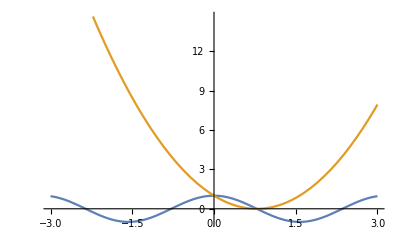

```mathematica
Plot[{f[x],g[x]},{x,-3,3}]
```

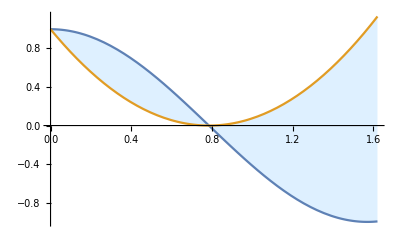

```mathematica
a = 0;
b = 16/π^2;
Plot[{f[x],g[x]},{x,a,b},Filling->{1->{{2},LightBlue}}]
```

```mathematica
Integrate[Abs[(16 (-Pi/4+x)^2)/Pi^2-Cos[2 x]],{x,0,Pi/4}]
```

(6-π)/12

```mathematica
Rešitev naloge 1.3
Najprej za lažjo predstavo narišemo graf in pogledamo, kaj moramo sploh izračunati. Ugotovimo, da moramo izračunati površino svetlega območja.
In to potem izračunamo z vgrajeno funkcijo Integrate.
```

```mathematica
Rešitev naloge 2.1
Iščemo verjetnost dogodka A, da je vsota števil na obeh zgornjih ploskvah 2, 3, ali 5. Ugodne možnosti so 1+1, 1+2, 2+1. 1+4, 4+1, 2+3 in 3+2, vseh skupaj 7. Vseh možnosti je 12*12 = 144.
Verjetnost dogodka A je torej (7/144).
```

```mathematica
N[Binomial[20,3]*(1/12)^3*(11/12)^17,3]
```

0.15

```mathematica
Rešitev naloge 2.2
Uporabimo formulo za Bernoullijevo zaporedje in omejimo število mest v rešitvi, takoj dobimo rezultat 0,150.
```

```mathematica
a = 6;
L= (12*5*a)/2;
Quantity[L, "Centimeters"]
P = N[12*(5 a^2)/(4 Sqrt[5-2 Sqrt[5]])];
Quantity[P, "Centimeters"*"Centimeters"]
```

180 cm

743.246 cm^2

```mathematica
Rešitev naloge 2.3
Najprej moramo izračunati število stranic. Ker je petkotnikov 12 in ima vsak 5 stranic je to 60 stranic, potem pa upoštevamo, da vsaka stranica povezuje 2 petkotnika in zato jih razpolovimo.
Potem poiščemo praktično formulo, s katero lahko izračunamo površino petkotnika kar s pomočjo stranice. Vstavimo notri dolžino stranice in pomnožimo z 12, ker ima dodekaeder ravno 12 petkotnikov.
```

```mathematica
Rešitev naloge 3.1
a_n = (e^2)^( n - 2) = e^(2n-2)
b_n = Log[a] = 2 n - 2;
Da dobimo diferenco, moramo odšteti n-ti člen od (n+1)-ga.
```

```mathematica
d = Simplify[(2*(n+1)-2) - (2*n -2)]
```

2

```mathematica
n = 100;
b1 = 0;
s = n/2*(2*b1 + (n-1)*d)
```

9900

```mathematica
Rešitev naloge 3.3
Za poljubna m in n iz naravnih števil velja
b_m = 2*m -2
b_n = 2*n -2
In ti dve števili v nobenem primeru nista tuji, saj sta obe deljivi z 2, ne glede na m in n.
```

```mathematica
Rešitev naloge 3.4
p_n(x) = 2x + 4x^2 + ... 2nx^n
V polinomu lahko izpostavimo 2x, ki je prisoten v vseh členih in dobimo
p_n(x) = 2x(1 + 2x + ... nx^(n-1))
Opazimo da je  (1 + 2x + ... nx^(n-1)) > 0 na intervalu od nič do neskončno, zato ta del ne prinese nobene ničle.
Ostane še 2x, ki ima na istem intervalu natanko eno ničlo x = 0, zato je to edina ničla na tem intervalu.
```

```mathematica
SetOptions[EvaluationNotebook[],Background-> Lighter[Lighter[Purple]]]
```